# Analysis of Rocky’s Runaway Behavior

In this notebook we’ll develop a better understanding of why your Rocky balances but tends to run away (i.e., velocity does not go to 0).

To start, we’ll define all of our transfer functions.

```mathematica
<<Notation`
Symbolize[OverHat[_]]
Symbolize[Subscript[_, _]]
```

```mathematica
Subscript[G, pwmtovelocity] = (a b)/(s+a);
Subscript[G, velocitytoangle] =s/(g-l s^2);
Subscript[G, thetaerrortopwm]= Subscript[K, p]+Subscript[K, i]/s;
Subscript[G, fullsystem]= Simplify[(Subscript[G, pwmtovelocity] Subscript[G, velocitytoangle] Subscript[G, thetaerrortopwm])/(1+Subscript[G, pwmtovelocity] Subscript[G, velocitytoangle] Subscript[G, thetaerrortopwm])]
```

(a b (K_i+K_p s))/(s (g-l s^2)+a (g+b K_i+b K_p s-l s^2))

## Re-examining our analysis of stability from class

Let’s plug in some values for all the constants and show that the poles of the transfer function are in the left half plane.  I’ll be using values of K_p=-600 and K_i=-6000, which several groups found to be stable.  The stability comes from both poles being in the left half plane.

```mathematica
constants = {g-> 98/10, l-> 0.2, Subscript[K, p]-> -600, Subscript[K, i]-> -6000, a-> 14, b-> 1/400};
Subscript[G, fullsystemsubbed]=Subscript[G, fullsystem]/.constants;
N[Solve[Denominator[Subscript[G, fullsystemsubbed]] ==0]]
```

{{s→-11.8658},{s→-1.06708-5.43485 ⅈ},{s→-1.06708+5.43485 ⅈ}}

## Come back Rocky!! Understanding why Rocky’s velocity doesn’t decay to 0

To understand Rocky’s runaway behavior, instead of looking at the poles of the transfer function of the full system (i.e., (θ(s))/(θ_d(s))), we need to look at the poles of (V(s))/(θ_d(s)).  By examining these poles we will be able to see why Rocky runs away.  Since we know (θ(s))/(θ_d(s)) from our prior analysis, all we have to do is multiply it by (V(s))/(θ(s)) to get (V(s))/(θ_d(s)).  (V(s))/(θ(s)) is simply the reciprocal of the transfer function of the pendulum block (1/G_velocitytoangle).  In this next block, we’ll examine the poles of this transfer function.

```mathematica
Subscript[G, thetadtovelocity]=Subscript[G, fullsystem] 1/Subscript[G, velocitytoangle];
N[Solve[Denominator[Subscript[G, thetadtovelocity]]==0,s]/.constants]
```

{{s→0.},{s→-11.8658},{s→-1.06708-5.43485 ⅈ},{s→-1.06708+5.43485 ⅈ}}

What you see from this analysis is that while all of the poles for (θ(s))/(θ_d(s)) are in the left half-plane, there is a pole for (V(s))/(θ_d(s)) that lies at the origin.  This pole of s = 0 will translate into a constant velocity offset that will not decay to 0 if you were to solve for the time domain function with some non-zero initial angle.

We can see this even more directly by setting the desired theta to a small value for a short duration (0.25 seconds).  This will cause the system to move from its unstable equilibrium and allow us to investigate the time domain response of the angle and the velocity.

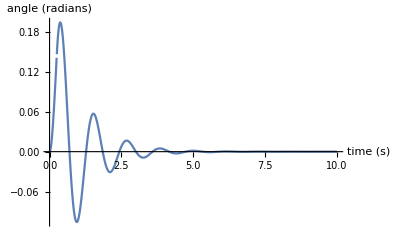

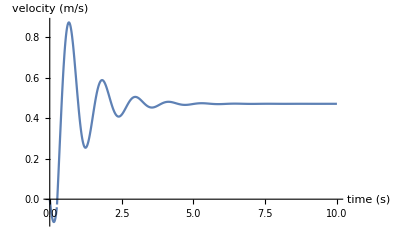

```mathematica
Subscript[θ, d][t]=(UnitStep[t]-UnitStep[t-1/4])/15;
thetaResponse =InverseLaplaceTransform[Subscript[G, fullsystemsubbed] LaplaceTransform[Subscript[θ, d][t],t,s],s,t];
vResponse =InverseLaplaceTransform[Subscript[G, fullsystemsubbed] LaplaceTransform[Subscript[θ, d][t],t,s]/(Subscript[G, velocitytoangle]/.constants),s,t];
Plot[thetaResponse,{t,0,10},PlotRange-> All,AxesLabel->{"time (s)", "angle (radians)"}]
Plot[vResponse,{t,0,10},PlotRange-> All,AxesLabel->{"time (s)", "velocity (m/s)"}]
```

## Preventing Runaway

There are several methods to prevent runaway in this system.  The controls book recommends adding a motor controller in the feedback loop.  This looks quite similar to the system we showed in the other notebook on coupled analysis (I can also post a Mathematica notebook on this as well).

This system won’t have the runaway behavior.  The analysis (taken from a Mathematica notebook from last year is shown below). (sorry for the repeated variable definitions, it would have taken a while to clean this up and it didn’t seem worth it).  (keep reading for another strategy after this one).

{J_p→480.,J_i→-3304.36,K_p→-2496.7,K_i→-16700.5}

1/600 (1/(49 π (81+4 π^2)^2)188200 ⅇ^(-10 (-1/4+t)) HeavisideTheta[-1/4+t] (198 π-8 π^3+1620 π (-1/4+t)+80 π^3 (-1/4+t)-198 ⅇ^(9 (-1/4+t)) π Cos[2 π (-1/4+t)]+8 ⅇ^(9 (-1/4+t)) π^3 Cos[2 π (-1/4+t)]+81 ⅇ^(9 (-1/4+t)) Sin[2 π (-1/4+t)]-76 ⅇ^(9 (-1/4+t)) π^2 Sin[2 π (-1/4+t)])+1/(49 (81+4 π^2)^2)11920 ⅇ^(-10 (-1/4+t)) π HeavisideTheta[-1/4+t] (198 π-8 π^3+1620 π (-1/4+t)+80 π^3 (-1/4+t)-198 ⅇ^(9 (-1/4+t)) π Cos[2 π (-1/4+t)]+8 ⅇ^(9 (-1/4+t)) π^3 Cos[2 π (-1/4+t)]+81 ⅇ^(9 (-1/4+t)) Sin[2 π (-1/4+t)]-76 ⅇ^(9 (-1/4+t)) π^2 Sin[2 π (-1/4+t)])+1/(π (81+4 π^2)^2)25960 ⅇ^(-10 (-1/4+t)) HeavisideTheta[-1/4+t] (-36 π-162 π (-1/4+t)-8 π^3 (-1/4+t)+36 ⅇ^(9 (-1/4+t)) π Cos[2 π (-1/4+t)]-81 ⅇ^(9 (-1/4+t)) Sin[2 π (-1/4+t)]+4 ⅇ^(9 (-1/4+t)) π^2 Sin[2 π (-1/4+t)])+1/((81+4 π^2)^2)1600 ⅇ^(-10 (-1/4+t)) π HeavisideTheta[-1/4+t] (-36 π-162 π (-1/4+t)-8 π^3 (-1/4+t)+36 ⅇ^(9 (-1/4+t)) π Cos[2 π (-1/4+t)]-81 ⅇ^(9 (-1/4+t)) Sin[2 π (-1/4+t)]+4 ⅇ^(9 (-1/4+t)) π^2 Sin[2 π (-1/4+t)])-1/(49 π (81+4 π^2)^2)188200 ⅇ^(-10 t) (198 π-8 π^3+1620 π t+80 π^3 t-198 ⅇ^(9 t) π Cos[2 π t]+8 ⅇ^(9 t) π^3 Cos[2 π t]+81 ⅇ^(9 t) Sin[2 π t]-76 ⅇ^(9 t) π^2 Sin[2 π t])-1/(49 (81+4 π^2)^2)11920 ⅇ^(-10 t) π (198 π-8 π^3+1620 π t+80 π^3 t-198 ⅇ^(9 t) π Cos[2 π t]+8 ⅇ^(9 t) π^3 Cos[2 π t]+81 ⅇ^(9 t) Sin[2 π t]-76 ⅇ^(9 t) π^2 Sin[2 π t])-1/(π (81+4 π^2)^2)25960 ⅇ^(-10 t) (-36 π-162 π t-8 π^3 t+36 ⅇ^(9 t) π Cos[2 π t]-81 ⅇ^(9 t) Sin[2 π t]+4 ⅇ^(9 t) π^2 Sin[2 π t])-1/((81+4 π^2)^2)1600 ⅇ^(-10 t) π (-36 π-162 π t-8 π^3 t+36 ⅇ^(9 t) π Cos[2 π t]-81 ⅇ^(9 t) Sin[2 π t]+4 ⅇ^(9 t) π^2 Sin[2 π t]))

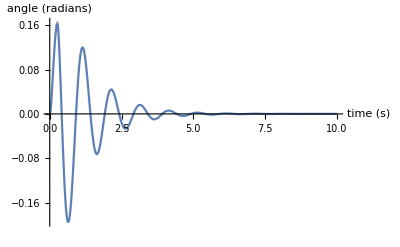

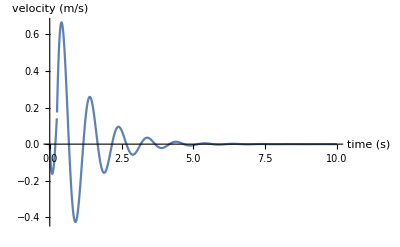

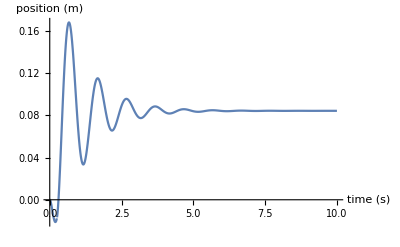

```mathematica
Subscript[G, MOTOR]= β α /(s+α);
Subscript[G, MOTORCONTROLLER]=Subscript[J, p]+Subscript[J, i]/s;
Subscript[G, CONTROLLEDMOTOR] = Factor[1/(1/Subscript[G, MOTOR]+Subscript[J, p]+Subscript[J, i]/s )];
Subscript[G, ANGLECONTROLLER]=Subscript[K, p]+Subscript[K, i]/s;
Subscript[G, VELOCITYTOANGLE]=-s/(L s^2- g);
Subscript[G, PLANT]=Factor[Subscript[G, CONTROLLEDMOTOR] Subscript[G, VELOCITYTOANGLE]];
Subscript[G, TOTALSYSTEM]=Factor[Subscript[G, ANGLECONTROLLER] Subscript[G, PLANT] / (1+Subscript[G, ANGLECONTROLLER] Subscript[G, PLANT])];
parameters = {g-> 98/10, L-> 1/5, α-> 10, β-> 1/400};
denominatorCoefs = CoefficientList[Denominator[Subscript[G, TOTALSYSTEM]/.parameters],s];
denominatorCoefs = denominatorCoefs/denominatorCoefs[[5]];

Subscript[p, 1] = -1 - 2π I;
Subscript[p, 2] = -1 + 2π I;
Subscript[p, 3]=-10;
Subscript[p, 4]=-10;

targetDenominator = (s-Subscript[p, 1])(s-Subscript[p, 2])(s-Subscript[p, 3])(s-Subscript[p, 4]);
targetDenominatorCoefficients = CoefficientList[targetDenominator,s];

controlParameters = Solve[denominatorCoefs[[1]]==targetDenominatorCoefficients[[1]] && denominatorCoefs[[2]] == targetDenominatorCoefficients[[2]] && denominatorCoefs[[3]] == targetDenominatorCoefficients[[3]] && denominatorCoefs[[4]] == targetDenominatorCoefficients[[4]],{Subscript[J, p],Subscript[J, i],Subscript[K, p], Subscript[K, i]}][[1]];
N[controlParameters]
Subscript[θ, d][t]=(UnitStep[t]-UnitStep[t-1/4])/15;

thetaOutputResponse = InverseLaplaceTransform[LaplaceTransform[Subscript[θ, d][t],t,s](Subscript[G, TOTALSYSTEM]/.parameters /.controlParameters),s,t]
vOutputResponse = InverseLaplaceTransform[LaplaceTransform[Subscript[θ, d][t],t,s] ((Subscript[G, TOTALSYSTEM]/Subscript[G, VELOCITYTOANGLE])/.parameters /.controlParameters),s,t];
xOutputResponse = InverseLaplaceTransform[LaplaceTransform[Subscript[θ, d][t],t,s]/s((Subscript[G, TOTALSYSTEM]/Subscript[G, VELOCITYTOANGLE])/.parameters /.controlParameters),s,t];
Plot[thetaOutputResponse,{t,0,10},PlotRange-> All,AxesLabel->{"time (s)", "angle (radians)"}]
Plot[vOutputResponse,{t,0,10},PlotRange-> All,AxesLabel->{"time (s)", "velocity (m/s)"}]
Plot[xOutputResponse,{t,0,10},PlotRange-> All,AxesLabel->{"time (s)", "position (m)"}]
```

A second strategy that a lot of students used last year was to feedback the velocity through an integrator that modulates the desired angle based on the integrated velocity (e.g., position).  This block diagram is shown below (source: Connor Novak and Jeremy Ryan’s Eye of the Tiger balancer).
-Graphics-

```mathematica
.
```